```mathematica
EmbedGraph5b[key_]:=Block[{val=allGraphs5[key], sets, reference={1,3,9,8,7}, g, sub},
sets=val["vertexsets"];
g=VertexDelete[ Graph[plantri[[20]]],2];
g=EdgeDelete[ g,{1<->3,3<->9,9<->8,8<->7,7<->1}];
Table[If[Length[s]>1,
g=VertexContract[g,Table[reference[[v]],{v,s}]]
], {s,sets}];
sub=val["graph"];
Table[
g=EdgeAdd[g,{reference[[First[sets[[e[[1]]]]]]]<->reference[[First[sets[[e[[2]]]]]]]}],{e,EdgeList[sub]}];

g
]
```

```mathematica
Select[VertexList[Graph[plantri[[20]],VertexLabels->"Name",GraphLayout->"PlanarEmbedding"]],VertexDegree[Graph[plantri[[20]],VertexLabels->"Name",GraphLayout->"PlanarEmbedding"],#]==5&]
```

{2,3,5,6,8,9,10,11,13,14,17,18}

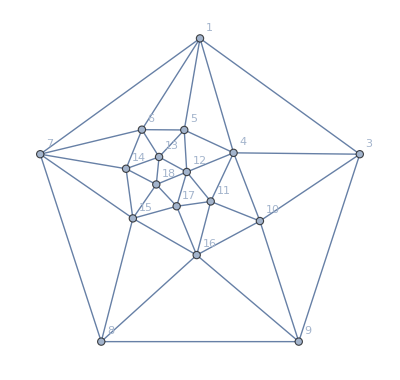

```mathematica
VertexDelete[Graph[plantri[[20]],VertexLabels->"Name",GraphLayout->"TutteEmbedding"],2]
```

```mathematica
Table[ChromaticPolynomial[EmbedGraph5b[k],x],{k,allGraphs5FakeAtomKeys}]//DeleteDuplicates//Length
```

52

```mathematica
Table[ChromaticPolynomial[EmbedGraph5b[k],x],{k,allGraphs5AtomKeys}]//DeleteDuplicates//Length
```

49

```mathematica
Table[ChromaticPolynomial[EmbedGraph5b[k],x],{k,allGraphs5NullAtomKeys}]//DeleteDuplicates//Length
```

47

```mathematica
Table[ChromaticPolynomial[EmbedGraph5b[k],x],{k,allGraphs5GeneratorAtomKeys}]//DeleteDuplicates//Length
```

52

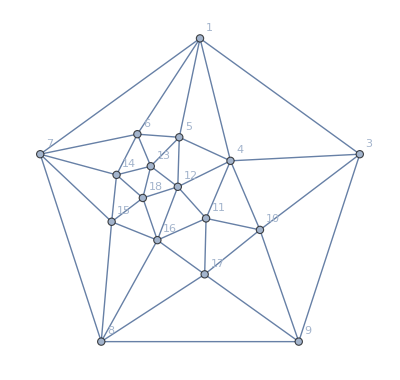

```mathematica
VertexDelete[Graph[plantri[[19]],VertexLabels->"Name",GraphLayout->"TutteEmbedding"],2]
```

```mathematica
EmbedGraph5c[key_]:=Block[{val=allGraphs5[key], sets, reference={1,3,9,8,7}, g, sub},
sets=val["vertexsets"];
g=VertexDelete[ Graph[plantri[[19]]],2];
g=EdgeDelete[ g,{1<->3,3<->9,9<->8,8<->7,7<->1}];
Table[If[Length[s]>1,
g=VertexContract[g,Table[reference[[v]],{v,s}]]
], {s,sets}];
sub=val["graph"];
Table[
g=EdgeAdd[g,{reference[[First[sets[[e[[1]]]]]]]<->reference[[First[sets[[e[[2]]]]]]]}],{e,EdgeList[sub]}];

g
]
```

```mathematica
Table[ChromaticPolynomial[EmbedGraph5c[k],x],{k,allGraphs5FakeAtomKeys}]//DeleteDuplicates//Length
```

52

```mathematica
Table[ChromaticPolynomial[EmbedGraph5c[k],x],{k,allGraphs5AtomKeys}]//DeleteDuplicates//Length
```

51

```mathematica
Table[ChromaticPolynomial[EmbedGraph5c[k],x],{k,allGraphs5NullAtomKeys}]//DeleteDuplicates//Length
```

50

```mathematica
Table[ChromaticPolynomial[EmbedGraph5c[k],x],{k,allGraphs5GeneratorAtomKeys}]//DeleteDuplicates//Length
```

52

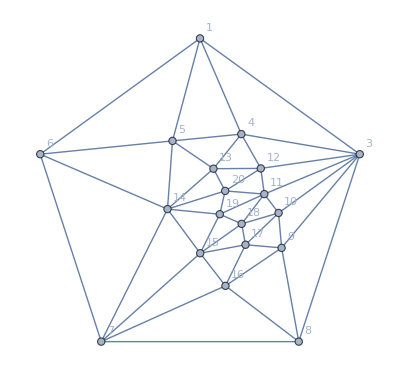

```mathematica
VertexDelete[Graph[plantri[[50]],VertexLabels->"Name",GraphLayout->"TutteEmbedding"],2]
```

```mathematica
EmbedGraph5d[key_]:=Block[{val=allGraphs5[key], sets, reference={1,3,8,7,6}, g, sub},
sets=val["vertexsets"];
g=VertexDelete[ Graph[plantri[[50]]],2];
g=EdgeDelete[ g,{1<->3,3<->8,8<->7,7<->6,6<->1}];
Table[If[Length[s]>1,
g=VertexContract[g,Table[reference[[v]],{v,s}]]
], {s,sets}];
sub=val["graph"];
Table[
g=EdgeAdd[g,{reference[[First[sets[[e[[1]]]]]]]<->reference[[First[sets[[e[[2]]]]]]]}],{e,EdgeList[sub]}];

g
]
```

```mathematica
Table[ChromaticPolynomial[EmbedGraph5d[k],x],{k,allGraphs5FakeAtomKeys}]//DeleteDuplicates//Length
```

52

```mathematica
Table[ChromaticPolynomial[EmbedGraph5d[k],x],{k,allGraphs5AtomKeys}]//DeleteDuplicates//Length
```

47

```mathematica
Table[ChromaticPolynomial[EmbedGraph5d[k],x],{k,allGraphs5NullAtomKeys}]//DeleteDuplicates//Length
```

46

```mathematica
Table[ChromaticPolynomial[EmbedGraph5d[k],x],{k,allGraphs5GeneratorAtomKeys}]//DeleteDuplicates//Length
```

52

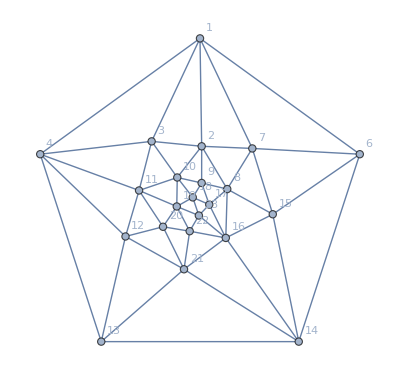

```mathematica
VertexDelete[Graph[plantri[[2000]],VertexLabels->"Name",GraphLayout->"TutteEmbedding"],5]
```

```mathematica
EmbedGraph5e[key_]:=Block[{val=allGraphs5[key], sets, reference={1,6,14,13,4}, g, sub},
sets=val["vertexsets"];
g=VertexDelete[ Graph[plantri[[2000]]],5];
g=EdgeDelete[ g,{1<->6,6<->14,14<->13,13<->4,4<->1}];
Table[If[Length[s]>1,
g=VertexContract[g,Table[reference[[v]],{v,s}]]
], {s,sets}];
sub=val["graph"];
Table[
g=EdgeAdd[g,{reference[[First[sets[[e[[1]]]]]]]<->reference[[First[sets[[e[[2]]]]]]]}],{e,EdgeList[sub]}];

g
]
```

```mathematica
Table[ChromaticPolynomial[EmbedGraph5e[k],x],{k,allGraphs5FakeAtomKeys}]//DeleteDuplicates//Length
```

52

```mathematica
Table[ChromaticPolynomial[EmbedGraph5e[k],x],{k,allGraphs5GeneratorAtomKeys}]//DeleteDuplicates//Length
```

52

```mathematica
Table[ShowGraph5Least[k],{k,Bases["F","Variables"]/.RepKey["F"]}]
```

{-Graphics-034,-Graphics-1968321,-Graphics-656124,-Graphics-218724,-Graphics-72921,-Graphics-24321,-Graphics-8124,-Graphics-2724,-Graphics-921,-Graphics-324,-Graphics-121,-Graphics-264878,-Graphics-219519,-Graphics-204398,-Graphics-1969213,-Graphics-1968615,-Graphics-1968413,-Graphics-87579,-Graphics-72939,-Graphics-664216,-Graphics-658816,-Graphics-656215,-Graphics-29178,-Graphics-243015,-Graphics-221416,-Graphics-219016,-Graphics-97213,-Graphics-81015,-Graphics-73813,-Graphics-3338,-Graphics-2739,-Graphics-24413,-Graphics-1099,-Graphics-8416,-Graphics-3615,-Graphics-138,-Graphics-287640,-Graphics-272460,-Graphics-264885,-Graphics-227080,-Graphics-219545,-Graphics-204485,-Graphics-196965,-Graphics-94900,-Graphics-87845,-Graphics-73745,-Graphics-66705,-Graphics-31605,-Graphics-24605,-Graphics-10625,-Graphics-3640,-Graphics-295240}

```mathematica
Table[ShowGraph5Least[k],{k,Bases["G","Variables"]/.RepKey["G"]}]
```

{-Graphics-295240,-Graphics-98410,-Graphics-229630,-Graphics-273370,-Graphics-287950,-Graphics-292810,-Graphics-294430,-Graphics-294970,-Graphics-295150,-Graphics-295210,-Graphics-295230,-Graphics-30371,-Graphics-75731,-Graphics-90851,-Graphics-98321,-Graphics-98381,-Graphics-98401,-Graphics-207671,-Graphics-222311,-Graphics-228820,-Graphics-229360,-Graphics-229621,-Graphics-266071,-Graphics-270941,-Graphics-273100,-Graphics-273340,-Graphics-285521,-Graphics-287141,-Graphics-287861,-Graphics-291911,-Graphics-292511,-Graphics-292801,-Graphics-294151,-Graphics-294400,-Graphics-294881,-Graphics-295111,-Graphics-7608,-Graphics-22788,-Graphics-30365,-Graphics-68168,-Graphics-75703,-Graphics-90765,-Graphics-98285,-Graphics-200348,-Graphics-207403,-Graphics-221503,-Graphics-228543,-Graphics-263645,-Graphics-270643,-Graphics-284625,-Graphics-291608,-Graphics-034}

```mathematica
Table[allGraphs5[k,"colofour"]//Length,{k,Bases["G","Variables"]/.RepKey["G"]}]//Total
```

357

```mathematica
Table[allGraphs5[k,"colofour"]//Length,{k,Bases["F","Variables"]/.RepKey["F"]}]//Total
```

1152

```mathematica
Table[allGraphs5[k,"colofour"]//Length,{k,Bases["E","Variables"]/.RepKey["E"]}]//Total
```

357

```mathematica
Table[allGraphs5[k,"colofourgenerator"]//Length,{k,Bases["C","Variables"]/.RepKey["C"]}]//Total
```

357